Version Date: 25 Jan 2023

# Cyanine Dye Regression Tutorial Student Handout

# Part I

## Objectives

Build regression models that predict the wavelength of maximum absorbance of different cyanine dyes.

Understand and apply different types of regression models, including simple linear regression, multiple regression, penalized regression, and tree models.

Use feature selection and the evaluation of feature importance to improve and interpret model performances.

Use regression model analysis as part of the scientific discovery process by generating hypotheses for factors that affect cyanine dye absorption.

Gain proficiency in reading and writing Mathematica code in a notebook environment.

## Getting started

If you have limited Mathematica experience, you may wish to watch this screencast (12 minutes) which will help you get started by introducing basic concepts, including entering input, understanding functions, working with data and matrix operations, and finding functions.  https://www.wolfram.com/broadcast/video.php?c=86&v=327

If you have experience in another programming language, the Fast Introduction for Programmers is a good way to get started https://www.wolfram.com/language/fast-introduction-for-programmers/en/

Mathematica notebooks consist of text cells (like this one) and program input and output cells like the ones below. An input cell is evaluated by typing Shift+Enter

## Basic of Mathematica

### Variables

Variables are reserved memory locations that store values.  Think of variables like a container that hold data which can be changed later in the program. For example to create a variable named “number” and assign its value as 100:

```mathematica
number = 100
```

100

This variable can be modified at any time:

```mathematica
number = 99
number = 1
```

99

1

The value of number has changed to 1:

```mathematica
number (*see what the value is now...*)
```

1

### Functions

Functions are sets of operations that take an action on some input.  Functions are defined using the delayed assignment (:=) operator, and the names of user-provided input values, called arguments, end with a underscore (“_”).  

For example, let’s define an absoluteValue function as below, which takes one argument, the number for which the absolute value should be calculated:

```mathematica
absoluteValue[num_]:=If[ 
(num ≥ 0), (*condition to check*)
num, (*if true, returns num*)
-num (*else, returns -num*)
]
```

Functions are called by providing their names, for example, the absolute value of 2 is:

```mathematica
absoluteValue[2]
```

2

And the absolute value of -4 is:

```mathematica
absoluteValue[-4]
```

4

Functions can also be applied using the `@` operator:

```mathematica
absoluteValue @ -4
```

4

This can be especially useful when we want to apply several functions sequentially to some input, such as:

```mathematica
Sqrt@Exp@Abs@Sin@Tan[0.2]
```

1.1059

This avoids having to write using a set of nested square brackets to achieve the same process:

```mathematica
Sqrt[Exp[Abs[Sin[Tan[0.2]]]]]
```

1.1059

### Advanced topics

The code below uses some other features of variables in Mathematica.  It is not necessary to review these now, but you may want to refer to this if you need to modify the code.

With defines a local constant.  It is often used in the definition of functions:

```mathematica
number =1 (*set number to 1 as an example*)

(* a private copy of `number` inside the with statement is set as 9, so t is assigned as 81*)
With[{number=9},t=number^2] 

number==1 (* global variable number is still 1*)
```

1

81

True

Lists can be used to store a series of values.  The list is defined by the curly brackets, {}.  Each entry in a List has an address that can be used to identify it.  We will see some list-like ways to access Datasets.

```mathematica
numberList  ={1, 2, -1, 1, -2.2, -42} (*here is an alternative way to declare a list*)
numberList[[5]] == -2.2 (*double square brackets used to access item in a list by index*)
```

{1,2,-1,1,-2.2,-42}

True

Map applies a function to every item in a list.  There are several different shortcuts for performing this operation, which can all be used interchangeably:

```mathematica
Map[absoluteValue, numberList] (* apply `absoluteValue` to every item in `numberList`*)
absoluteValue /@ numberList (*`/@` is a shortcut for `Map`*)
Map[absoluteValue]@numberList (*operator style way of Maping a function on a list *)
```

{1,2,1,1,2.2,42}

{1,2,1,1,2.2,42}

{1,2,1,1,2.2,42}

Arrows denote a Rule; these are often used to define replacement processes of other relations.  The rule symbol →  is entered by typing the characters  “->” (the notebook will convert it).  Rules have a number of applications, such as replacement patterns

```mathematica
exampleRule=x->-1 (*give pattern `x`, return -1*)
x^2+y+1 /.exampleRule (*replace `x` in the preceeding expression with -1, the operator `/.` means applying the rule*)
```

x→-1

2+y

5.  Rules are also often used to denote optional arguments to functions.  For example:

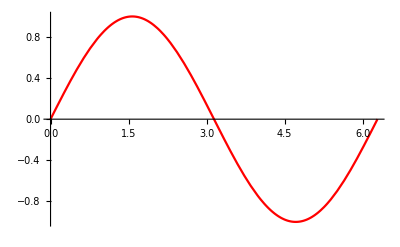

```mathematica
Plot[Sin[x],{x,0,2 Pi}, PlotStyle->Red]
```

5.  Associations (sometimes called ‘dictionaries’ in other programming languages) organize groups of entries in terms of key-value pairs; this is especially useful when there is no numerical ordering implied, but we still want to group data together.  For example, our keys will be names of fruits in English, and the values are the corresponding names in Spanish:

```mathematica
translate=<|"apple"->"manzana", "orange"->"naranja"|>; (*define a dictionary*)
```

We can access the entries by the key name, analogous to entries in a list:

```mathematica
translate["apple"]
```

manzana

We can also access lists of the keys and value, by applying the relevant functions to the association.

```mathematica
Keys[translate]
Values[translate]
```

{apple,orange}

{manzana,naranja}

A Map performed on an Association return a new Association where the keys are the same and the functions are applied to the values

```mathematica
(*define an example function*)
lookupImage[name_]:=First@ WebImageSearch[name,"Thumbnails",1]

(*Map applies the function to each value in the Association*)
Map[lookupImage]@translate
```

<|apple→-Graphics-,orange→-Graphics-|>

7. The symbol % fills in the last output and the symbol %% fills in the second-to-last output.  This can be useful in sequential processes.

```mathematica
Sin[1]
%+2
%%+3
```

Sin[1]

2+Sin[1]

3+Sin[1]

8.  In addition to using the many built-in Mathematica functions (described in the Help browser), it is sometimes useful to make use of user-contributed functions in the Wolfram Function Repository.  These are accessed by using the ResourceFunction function, followed by a name, and any relevant arguments:

```mathematica
ResourceFunction["PlayingCardGraphic"][{5,6,11}]
(*change the numbers, run the function again,and see what happens!*)
```

-Graphics-

## Get and Preprocess the Data

Now let’s load in the train and test datasets, which are stored on GitHub (a repository for storing and sharing data and software code).  We will use the Import function to read this as a Dataset:

```mathematica
(* load the datasets from GitHub *)
dataset1=Import[
"https://raw.githubusercontent.com/elizabeththrall/MLforPChem/main/MLcyaninedye/Data/cyaninedye_dataset_part1.csv",
"Dataset",HeaderLines->1];

dataset2=Import[
"https://raw.githubusercontent.com/elizabeththrall/MLforPChem/main/MLcyaninedye/Data/cyaninedye_dataset_part2.csv",
"Dataset",HeaderLines->1];

dataset3=Import["https://raw.githubusercontent.com/elizabeththrall/MLforPChem/main/MLcyaninedye/Data/cyaninedye_dataset_part3.csv","Dataset",HeaderLines->1];

(*Merge the datasets, delete duplicates,and drop features*)

dataset = KeyDrop[{"Chi0n","Chi1n","Chi2n","Chi3n","Chi4n"}]@ DeleteDuplicates@Join[dataset1,dataset2,dataset3];
```

Import::nfurl: Unable to retrieve data from https://raw.githubusercontent.com/elizabeththrall/MLforPChem/main/MLcyaninedye/Data/cyaninedye_dataset_part1.csv. Consult Internal`$LastInternalFailure for potential information.

Import::nfurl: Unable to retrieve data from https://raw.githubusercontent.com/elizabeththrall/MLforPChem/main/MLcyaninedye/Data/cyaninedye_dataset_part2.csv. Consult Internal`$LastInternalFailure for potential information.

Import::nfurl: Unable to retrieve data from https://raw.githubusercontent.com/elizabeththrall/MLforPChem/main/MLcyaninedye/Data/cyaninedye_dataset_part3.csv. Consult Internal`$LastInternalFailure for potential information.

Join::normal: Nonatomic expression expected at position 1 in Join[$Failed].

KeyDrop::invrl: The argument Join[$Failed] is not a valid Association or a list of rules.

(Note that Import can be used to import data from anywhere, including files on your local computer; here we are reading it from an internet URL).

Let’s see what these data look like. You can display the current contents of a variable by entering its name and executing the cell:

```mathematica
dataset (*display the contents of the variable "dataset*)
```

Take a look at the structure of this variable (you may need to use the scroll buttons to see each row and column, depending on your screen size):

Each row contains data for a different molecule

The first column contains the molecule SMILES string. SMILES is an unique chemical identifier in the form of an ASCII string.

The second column contains the molecule InChIKey. InChIKey is another unique chemical identifier in the form of an ASCII string.

The next 13 columns contain different molecular features (described below). These are the variables that we will use to predict the wavelength of maximum absorbance. Features are sometimes called "independent" or "predictor" variables.

The final column contains the wavelength of maximum absorbance (MaxAbsorbanceWavelength) for each molecule. This is the target variable that we want to predict (sometimes called the “dependent” or “response” variable).

Features:
Our regression analysis will use the 13 features below, which were computed for each molecule in the dataset.

AromaticRingCount: Number of aromatic rings in the molecule

HBondDonorCount: Number of hydrogen bond donors in the molecule

HBondAcceptorCount: Number of hydrogen bond acceptors in the molecule

FractionCarbonSP3: Fraction of carbon atoms in the molecule with sp3 hybridization

HeteroatomCount: Total number of heteroatoms (i.e., atoms other than carbon) in cyclic rings in the molecule

HeterocycleCount: Total number of heterocyclic rings (i.e., rings containing atoms other than carbon) in the molecule

RotatableBondCount: Number of bonds that can be rotated in the molecule (i.e., the number of non-cyclic sp3 bonds)

MolecularMass: Mass of the molecule

DegreeOfUnsaturation: Total number of pi bonds and rings in the molecule

MinEllipsoidLength: the major axis length of the smallest volume ellipsoid that could contain the molecule

MaxDistance: the largest distance between any pair of atoms in the molecule

LongestPiChain: longest continuous path of conjugated pi bonds

LinkerLength: longest conjugated pi chain that is not part of a ring

Sometimes removing outliers from the dataset can help improve model performance.  Outliers are data points that differ drastically from the rest of the observations. Machine Learning models generalize from training data to make predictions; if they learn from data with extreme outliers, they may perform worse.

https://en.wikipedia.org/wiki/Outlier

It is always useful to identify possible outliers by charting a Histogram of the data.  (The option PlotRange is set to All, as otherwise Mathematica will focus the attention of the plot on the region with the most information.)

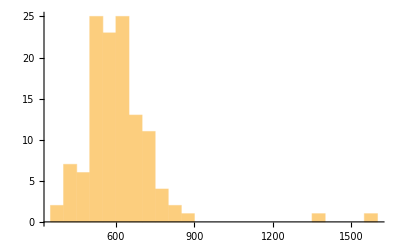

```mathematica
Histogram[
dataset[All,"MaxAbsorbanceWavelength"],
PlotRange->All]
```

Notice the outliers; these are unlikely to be well represented by our data.  We will automatically process the  dataset, analysing it for anomalies, and then resetting the dataset variable to have the “anomaly free” values:

```mathematica
dataset=DeleteAnomalies[dataset]
```

(A companion function, FindAnomalies could be used to extract these anomalies for further investigation and visualization). DeleteAnomalies has removed 6 anomalous data points, including the outliers that we had previously observed in the histogram:

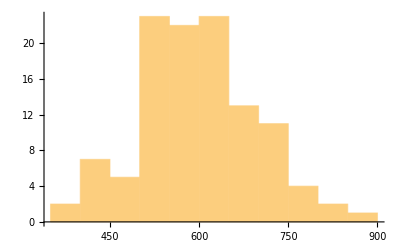

```mathematica
Histogram[
dataset[All,"MaxAbsorbanceWavelength"],
PlotRange->All]
```

### Data Selection with Structured Datasets

A tabular dataset can be thought of as storing a collection of values in a rectangular “grid”.  We can see the size of that grid using the Dimensions function:

```mathematica
Dimensions[dataset](*shape of dataset?*)
```

{113,16}

(Note:  You can always learn more about built-in Mathematica functions by typing ? followed by the function name.  Clicking the “i” button in the upper right hand corner gives more information:

```mathematica
?Dimensions
```

We will often need to access the values stored in particular positions in a variable. We can do this by specifying the indices corresponding to that position:

variable[[row, column]] extracts the value at the specified row and column.

Note the two square brackets (access the elements in a list of data) as opposed to the single brackets used to specify the arguments to a function.

“;;” species a range of values.

“All” specifies that we should take all of the values along a dimension.

We can also count the indices from the “end” using negative numbers, e.g., variable[[-2]] returns the second-from-last element.

Note that in Mathematica, index values start from 1 (instead of 0 like some other programming languages such as C and Python).

For example:

dataset[[2;;3, 1]]  take rows 2 and 3 and the first column

dataset[[ All, 1]]   take all rows and the first column

dataset[[All, 3;;5]]  take all rows and third through fifth columns

Try the following examples.  Can you predict what the output will be?

```mathematica
dataset[[1]] (*access an entry by its indices, using double square brackets*)
```

```mathematica
dataset[[1,1]](*access entry by its indices, using double square brackets*)
```

Join[$Failed]

```mathematica
dataset[[1;;3, 1;;10]](*get first 3 rows and the first 10 columns using `;;`*)
```

Part::take: Cannot take positions 1 through 3 in DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]].

DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]]⟦1;;3,1;;10⟧

```mathematica
(* predict what the output of this line of code will be *)
dataset[[1;;3,1;;3]]
```

Part::take: Cannot take positions 1 through 3 in DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]].

DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]]⟦1;;3,1;;3⟧

The columns in datasets can also be addressed by name.  For example, the SMILES column in the first few rows:

```mathematica
dataset[[1;;3,"SMILES"]]
```

Part::take: Cannot take positions 1 through 3 in DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]].

DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]]⟦1;;3,SMILES⟧

This can also be generalized to select a collection of columns  by providing a list as input:

```mathematica
dataset[[1;;3,{"MolecularMass","MaxAbsorbanceWavelength"}]]
```

Part::take: Cannot take positions 1 through 3 in DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]].

DeleteAnomalies[KeyDrop[{Chi0n,Chi1n,Chi2n,Chi3n,Chi4n}][Join[$Failed]]]⟦1;;3,{MolecularMass,MaxAbsorbanceWavelength}⟧

### Visualizing molecular structure

To continue familiarizing ourselves with the dataset, we can visualize the structures of the different cyanine dyes.  Before we do so, let’s first get a quick overview of making and plotting molecules in general in Mathematica.  The Molecule function can take input names (either in machine-readable SMILES or human-readable IUPAC name) and covert them into a machine representation:

```mathematica
mol=Molecule["CN(C)C(=N)N(C)C"]
```

Molecule[…]

The MoleculePlot function takes a Molecule as an input and returns a two-dimensional figure:

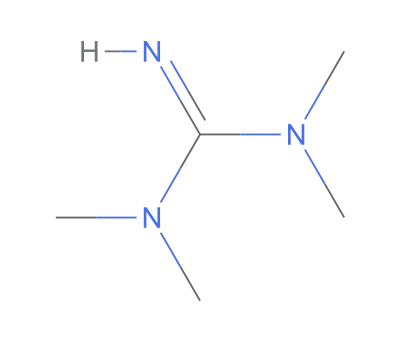

```mathematica
MoleculePlot[mol]
```

What do you think MoleculePlot3D does?  (After you run the code below, be sure to click and drag the result to rotate the molecule!)

```mathematica
MoleculePlot3D[mol]
```

-Graphics3D-

(One caveat: this structure is not necessarily the true 3D structure of the molecule, rather it is the result of a molecular mechanics calculation, selecting a single random conformer.)

Now let’s use these tools to visualize some of the molecules in our dataset.  The code block below displays the structure of the molecule in the row of our dataset corresponding to the specified molIdx variable. Try changing molIdx to visualize the structure of a few different molecules:

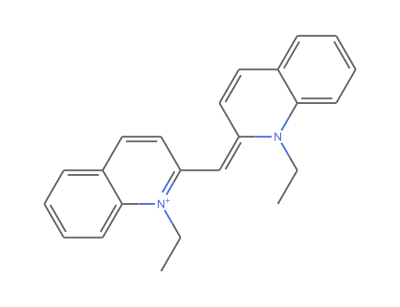

```mathematica
molIdx=1;  (* index value corresponding to the row in our dataset *)
MoleculePlot@Molecule@dataset[[molIdx,1]] (* display the molecule in row molIdx *)
```

Alternatively, we can display a random sample of molecules in the dataset. Run the first code block below to define an accessory function, then run the second one to display a random selection of 5 molecular structures from the dataset:

```mathematica
(* define a function to perform the sequence of operations *)
plotMolecules[smiles_]:=MoleculePlot@Molecule[smiles]
```

```mathematica
(* apply the function to a random sample of 5 molecules *)
Map[plotMolecules]@RandomSample[dataset[[All,1]],5]
```

Run the code block above to visualize a few different sets of molecular structures; each time you run the code, it will select a different RandomSample.  How similar are the molecular structures in the dataset? Are there any common structural features? Do you notice any closely-related molecules in the dataset?

### Identifying dependent (y) and independent variables (X)

Next we need to split our dataset into dependent and independent variables. An independent variable does not depend on other variables, whereas a dependent variable is affected by independent variables and changes accordingly. Independent and dependent variables are commonly indicated as X and y:

X is an array of independent variables

y is the dependent variable

In regression analysis, the dependent variables that we want to predict is referred to as a target value. In our dataset, MaxAbsorbanceWavelength is the target value (i.e., the dependent variable, y), and the 13 features are the independent variables (i.e., X). We will omit the non-numerical variables in our dataset (the SMILES and InChIKey molecular identifiers).

```mathematica
xyPairs =With[
{noIdentifiers=KeyDrop[{"SMILES","InChIKey"}]@dataset},
 ResourceFunction["TableToTrainingSet"][ noIdentifiers,"MaxAbsorbanceWavelength"]
];
```

The output is in the form of a list of Association --> value rule pairs.  Let us display the first two below:

```mathematica
xyPairs[[1;;2]]
```

{<|AromaticRingCount→3,HBondDonorCount→0,HBondAcceptorCount→1,FractionCarbonSP3→0.173913,HeteroatomCount→2,HeterocycleCount→2,RotatableBondCount→3,MolecularMass→327.451,DegreeOfUnsaturation→13,MinEllipsoidLength→121.73,MaxDistance→13.5031,LongestPiChain→12,LinkerLength→2|>→529,<|AromaticRingCount→3,HBondDonorCount→0,HBondAcceptorCount→1,FractionCarbonSP3→0.16,HeteroatomCount→2,HeterocycleCount→2,RotatableBondCount→4,MolecularMass→353.489,DegreeOfUnsaturation→14,MinEllipsoidLength→324.768,MaxDistance→16.7576,LongestPiChain→14,LinkerLength→4|>→626}

### Split Train & Test Data

We will use most of our dataset to train our regression models; this portion is the “training” dataset. To evaluate model performance, however, we will need a test dataset.  We will randomly split our data into a training and test set; by default this function does an 80/20% split with a random shuffle of the items.  (Note that because this train/test split is random, you will find that the regression results vary each time you run the notebook.)

```mathematica
{train,test}=ResourceFunction["TrainTestSplit"]@xyPairs;
```

### Data Scaling

Notice that our features span a wide range of different values, from less than 1 to greater than 100. Many machine learning models perform better when the variables are on the same scale, so it’s usually a good practice to rescale features before performing the analysis.

https://en.wikipedia.org/wiki/Feature_scaling

There are many methods that can be used to scale data. Two approaches are:

Scaling: Scale our features in a specified range (e.g., between 0 and 1) without altering the distribution shape

Normalizing: Scale our features, usually altering the distribution shape

For this analysis, let’s scale all of our features to range between 0 and 1, based on the minimum and maximum of the training set.  The functions minMaxFit and minMaxTransform, defined below, accomplish this task.  You do not need to modify these functions.

```mathematica
minMaxFit[d_List]:=With[
{featureNames = Keys@First@Keys[d],
minMaxPairs=MinMax/@Transpose@Values@Keys[d]},
AssociationThread[featureNames->minMaxPairs]]

rescale[{x_,minMax_List}]:=N@Rescale[x,minMax]
minMaxTransform[scale_Association][x_Association->y_]:=Merge[{x,scale},rescale]->y
minMaxTransform[scale_Association][l_List]:=minMaxTransform[scale]/@l
```

We begin by determining the maximum and minimum of each feature:

```mathematica
scale=minMaxFit[train]
```

<|AromaticRingCount→{2,4},HBondDonorCount→{0,4},HBondAcceptorCount→{1,15},FractionCarbonSP3→{0,0.465116},HeteroatomCount→{2,20},HeterocycleCount→{0,4},RotatableBondCount→{2,22},MolecularMass→{305.357,936.051},DegreeOfUnsaturation→{11,23},MinEllipsoidLength→{97.2958,4405.33},MaxDistance→{10.8945,26.2652},LongestPiChain→{7,19},LinkerLength→{1,10}|>

Then we can apply this to transform the training and test sets to have input features between 0 and 1.  (Be careful,  as this will replace the values in these datasets with the rescaled versions. You should only run this code once. If you accidentally run it twice, go back and regenerate the training and test sets in the section Split Train & Test Data.)

```mathematica
train=minMaxTransform[scale][train];
test=minMaxTransform[scale][test];
```

```mathematica
train[[1;;2]] (*visualize the first few as an example*)
```

{<|AromaticRingCount→0.,HBondDonorCount→0.25,HBondAcceptorCount→0.5,FractionCarbonSP3→0.186957,HeteroatomCount→0.444444,HeterocycleCount→0.,RotatableBondCount→0.15,MolecularMass→0.256977,DegreeOfUnsaturation→0.583333,MinEllipsoidLength→0.00400188,MaxDistance→0.0205604,LongestPiChain→0.25,LinkerLength→0.111111|>→429,<|AromaticRingCount→0.5,HBondDonorCount→0.,HBondAcceptorCount→0.0714286,FractionCarbonSP3→0.358333,HeteroatomCount→0.0555556,HeterocycleCount→0.5,RotatableBondCount→0.05,MolecularMass→0.0778825,DegreeOfUnsaturation→0.25,MinEllipsoidLength→0.0314506,MaxDistance→0.178017,LongestPiChain→0.5,LinkerLength→0.111111|>→593}

Note that none of the feature values in the training dataset are smaller than 0 or greater than 1 now.

## Building Regression Models

Regression analysis is a process of explaining and defining the relationship between dependent and independent variables. In this activity, we will train several regression models to predict our target value, MaxAbsorbanceWavelength (in this section and later in the Penalized Regression and Tree Models sections). We will use different metrics to evaluate how well the models perform (in the Model Evaluation section). By choosing better independent variables (in the Feature Selection section) we can try to improve our model performance. Finally, we can interpret our models and gain insight into what features are important (in the Feature Importance section).

### Simple Linear regression

Let’s start with the most basic type of regression model. Simple linear regression is a method that tries to define the relationship between two variables, the dependent variable and a single independent variable.

https://en.wikipedia.org/wiki/Simple_linear_regression

https://jakevdp.github.io/PythonDataScienceHandbook/05.06-linear-regression.html

This relationship can be represented by a well-fitted line that follows:

y=β_0+β_1 x

where:

β_0: y-intercept
β_1: slope (called the coefficient or weight in this context)

The optimal slope is generally determined by minimizing the residual sum of squares (RSS), which is given by:

where y_i are the actual values and ŷ_i are the model predictions. This approached is referred to as the ordinary least squares (OLS) method.  You can read more about these methods at the following links:

https://en.wikipedia.org/wiki/Residual_sum_of_squares

https://en.wikipedia.org/wiki/Ordinary_least_squares

Now that we know how a simple linear regression model works, let’s train our first machine learning model by selecting one feature from our set of independent variables and plotting the line that best describes the relationship between our selected feature and the dependent variable (Max Absorbance Wavelength).

First let’s define some convenience functions for extracting a single feature.  Again,  you do not need to modify these functions, but we will use them in the subsequent code:

```mathematica
(*extract a name from a single row*)
extractSingleFeature[name_String][x_Association->y_]:=Lookup[x,name]->y

(*apply to the entire dataset*)
extractSingleFeature[name_String][data_List]:=Map[extractSingleFeature[name],data]

(*convenience functions for plotting*)
toXY[x_->y_]:={x,y}
toXY[data_List]:=Map[toXY,data]
```

Because we’ll be working with a few different simple linear regression models, we can use associations (see the Basics of Mathematica section) to store the training and test data for each model, as well as the trained models. First initialize the empty variables (only run this code block once):

```mathematica
(*create empty associations*)
singleFeatureTrain=Association[]; (*single-variable training data*)
singleFeatureTest=Association[]; (*single-variable test data*)singleFeatureModels = Association[];(*simple linear regression models*)
```

Let’s start by choosing the FractionCarbonSP3 feature and seeing how well it predicts the MaxAbsorbanceWavelength. Run the code block below to select the feature, extract the training and testing data for that feature, and train the regression model. (Note that to run a simple linear regression with another feature, you can simply copy this code block and change the featureName variable.)

```mathematica
(*select a single feature*)
featureName="FractionCarbonSP3";

(*save the training and test data for that feature in the corresponding association variables*)
singleFeatureTrain[featureName]=extractSingleFeature[featureName]@train;
singleFeatureTest[featureName]=extractSingleFeature[featureName]@test;

(*train a simple linear regression for that feature and save it to the association variable*)
singleFeatureModels[featureName]=Predict[singleFeatureTrain[featureName],Method->"LinearRegression"]
```

PredictorFunction[…]

It is useful to summarize the quality of our fit by using the PredictorMeasurements function.  To get a summary of the model performance, we provide this function with two inputs: the trained regression model and the data (comprised of x-y pairs) on which it is to be evaluated. Let’s start by looking at the performance of the model on the training dataset:

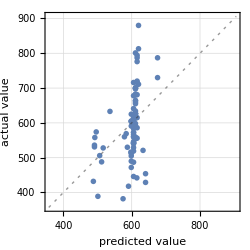
Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 90
Standard deviation | 89.7 ± 7.2
Standard deviation baseline | 98.4 ± 7.6
R-squared | 0.169 ± 0.19
Mean cross entropy | 5.92 ± 0.079
Single evaluation time | 3.32 ms/example
Batch evaluation speed | 877. examples/s
-Graphics- |

```mathematica
PredictorMeasurements[singleFeatureModels[featureName],singleFeatureTrain[featureName]]
```

The graph above plots the actual wavelength vs. the predicted wavelength for the training data. If the model could perfectly explain the variation in the training data, all the blue dots would lie along the dashed line. Clearly the model is not perfect.

It can also be useful to examine the correlation between the feature used to the train the regression model and the target value. Let’s plot the actual MaxAbsorbanceWavelength as a function of the value of FractionCarbonSP3.

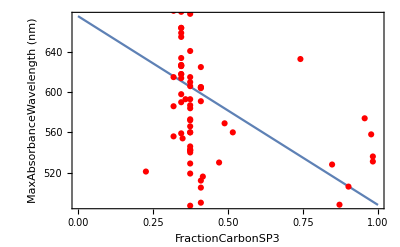

```mathematica
(*Plot a graphical representation*)
Show[
Plot[
singleFeatureModels[featureName][x],{x,0,1},(*evaluate the model on inputs ranging from the lowest to the highest value*)
FrameLabel->{"FractionCarbonSP3","MaxAbsorbanceWavelength (nm)"},
Frame->True],
ListPlot[toXY[singleFeatureTrain[featureName]],PlotStyle->Red](*plot the training data points*)
]
```

If FractionCarbonSP3 could explain all the variation in MaxAbsorbanceWavelength, the red dots would lie along the blue line. Again we can see that the regression model is not perfect. In particular, many data points have FractionCarbonSP3 ≈ 0.4 but very different MaxAbsorbanceWavelength values.

Now that we’ve evaluated the model performance with the training dataset, let’s use this model to predict MaxAbsorbanceWavelength for the test dataset and compare our predicted wavelengths to the true values. This is the real test of the model’s performance.

Run the code block below to perform this analysis and generate a plot of actual vs. predicted wavelength.

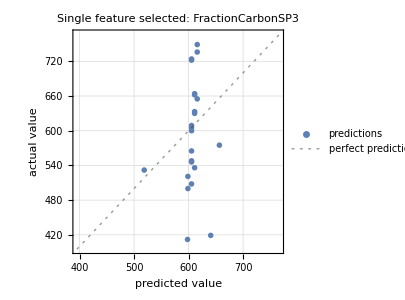

```mathematica
Show[
PredictorMeasurements[singleFeatureModels[featureName],singleFeatureTest[featureName],"ComparisonPlot"],
PlotLabel->"Single feature selected: "<>featureName]
```

If the model predictions were perfect, all the blue dots would lie along the dashed line. As we saw before, this model is not perfect. There are quantitative ways that we can evaluate the performance of the model, which we’ll discuss soon.

For now, go back to the description of the different molecular features in our dataset. Use your chemical intuition and think about which ones might be correlated with MaxAbsorbanceWavelength. Then write new code to perform and visualize a linear regression for a different variable. (Hint: you can copy the code blocks above and modify them to choose a different feature and save a new model. Name the variables singleFeatureTrain2, singleFeatureTest2, and regressor2 to avoid overwriting the previous model.)

ADD A CODE BLOCK HERE TO PERFORM A SIMPLE LINEAR REGRESSION FOR A DIFFERENT VARIABLE

### Multiple Regression

When we have more than one independent variable in our dataset, we can make use of a multiple regression model. A multiple regression model can perform better at predicting the value of a dependent variable since the model has more information to use.

https://en.wikipedia.org/wiki/Linear_regression#Simple_and_multiple_linear_regression

The formula is an extension of the single-variable simple linear regression:

y=β_0+β_1 x_1+β_2 x_2+...+β_k x_k

where:

β_0: y-intercept
β_k: slope corresponding to the k^th feature
k: number of independent features used in the model

As for the simple linear regression, the optimal slopes are determined by minimizing the RSS.

Now let’s perform a multiple linear regression using all 13 molecular features and plot the actual vs. predicted wavelength:

```mathematica
(*train a multiple regression model without any regularization (more on that later)*)
multipleRegression=Predict[train,
Method->{"LinearRegression","L1Regularization"->0,"L2Regularization"->0}]
```

PredictorFunction[…]

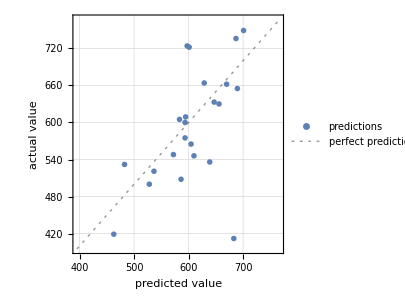

```mathematica
PredictorMeasurements[multipleRegression,test,"ComparisonPlot"]
```

As for the single-variable case, perfect model performance would be indicated by all the blue dots lying along the dashed line. Although this model isn’t perfect, its performance looks qualitatively better than the FractionCarbonSP3 simple linear regression, and the predicted wavelengths span a wider range of values. Thus we can see that providing the model with more information improved the performance, as expected.

### Model Evaluation

By plotting predicted vs. actual wavelength, we could make a qualitative assessment of model performance. But how can we quantify the performance of a particular model, or quantitatively compare two different models? To do this, we can evaluate performance metrics using our test data.

Let’s consider the following four metrics to quantify the agreement between our model predictions (ŷ_i) and the actual values (y_i):

Mean Absolute Error (MAE): MAE is the average of the absolute difference between the actual and predicted values. The lower the error, the better the model performance.
https://en.wikipedia.org/wiki/Mean_absolute_error

Mean Squared Error (MSE): MSE is the average of the squared difference between the actual and predicted values. As before, the lower the error, the better the model performance. MSE is one of the most used metrics for this kind of model.
https://en.wikipedia.org/wiki/Mean_squared_error

Root Mean Squared Error (RMSE): RMSE is the square root of the MSE. As before, the lower the error, the better the model performance. It is conceptually similar to the standard deviation.
https://en.wikipedia.org/wiki/Root-mean-square_deviation

Coefficient of Determination (R^2): R^2 reports how well the model is fitted to the data by comparing it to the average line of the dependent variable. In other words, it measures the degree to which the model explains the variability of the observed data. For example, a coefficient of determination of 80% indicates that the regression model explains 80% of the variability seen in the dependent variable.
https://en.wikipedia.org/wiki/Coefficient_of_determination

Although these quantitative metrics are informative, it is a good practice to see how the data behave with our own eyes through data visualization. Sometimes a single number or metric cannot explain the whole picture, or can even be misleading. (Anscombe’s quartet is a famous illustration of that point: https://en.wikipedia.org/wiki/Anscombe%27s_quartet

Mathematica has built-in functions for calculating a number of different metrics.  Let’s see what properties are available:

```mathematica
PredictorMeasurements[multipleRegression,test,"Properties"]
```

{BatchEvaluationTime,BestPredictedExamples,ComparisonPlot,EvaluationTime,Examples,FractionVarianceUnexplained,GeometricMeanProbabilityDensity,ICEPlots,LeastCertainExamples,Likelihood,LogLikelihood,MeanCrossEntropy,MeanDeviation,MeanSquare,MostCertainExamples,Perplexity,PredictorFunction,ProbabilityDensities,ProbabilityDensityHistogram,Properties,RejectionRate,Report,ResidualHistogram,ResidualPlot,Residuals,RSquared,SHAPPlots,SHAPValues,StandardDeviation,StandardDeviationBaseline,TotalSquare,WorstPredictedExamples}

We can request a single property using the code below:

```mathematica
PredictorMeasurements[multipleRegression,test,"MeanSquare"]
```

6153.74

We can also request multiple properties at the same time:

```mathematica
PredictorMeasurements[multipleRegression,test,{"MeanDeviation","MeanSquare","StandardDeviation","RSquared"}]
```

{53.8988,6153.74,78.4458,0.263031}

Let’s make life easy by defining a convenience function that takes the model and a test set and calculates our four metrics of interest:

```mathematica
modelEvaluation[model_,testSet_]:=With[
{properties={"MeanDeviation","MeanSquare","StandardDeviation","RSquared"}},
AssociationThread[properties->PredictorMeasurements[model,testSet,properties]]]
```

Now we can store these results in a variable called metrics and add the results for the simple linear regression and multiple regression models. First initialize the empty metrics variable (only run this code block once):

```mathematica
metrics=Association[]; (*create an empty association to store results*)
```

Then we can add the results for the models tested to the metrics variable. (Note that we have to provide the appropriate test dataset for each model.)

```mathematica
(*calculate the performance metrics for the FractionCarbonSP3 simple linear regression using the corresponding single-variable test data*)
metrics["Simple LR (FractionCarbonSP3"]=modelEvaluation[singleFeatureModels[featureName],singleFeatureTest[featureName]] 

(*calculate the performance metrics for the multiple regression using the full test data*)
metrics["Multiple LR"]=modelEvaluation[multipleRegression,test]
```

<|MeanDeviation→73.5022,MeanSquare→8587.7,StandardDeviation→92.6698,RSquared→-0.0284573|>

<|MeanDeviation→53.8988,MeanSquare→6153.74,StandardDeviation→78.4458,RSquared→0.263031|>

We can use the Dataset command to organize the metrics into a tabular format:

```mathematica
Dataset[metrics] (*pretty print the results*)
```

When we compare the FractionCarbonSP3 simple linear regression and the multiple regression, we can see that multiple regression works better according to both the eye test and the quantitative performance metrics.

Now add a code block below to calculate these performance metrics for a simple linear regression with the single feature that you tested above, add them to the metrics variable, and display the results in table. How did your new model perform?

ADD A CODE BLOCK HERE TO CALCULATE THE PERFORMANCE METRICS FOR A SIMPLE LINEAR REGRESSION USING A DIFFERENT VARIABLE AND ADD THEM TO THE METRICS TABLE

## Avoiding Model Overfitting

Overfitting refers to a situation when a model has become too specific to the training data and fails to generalize well to new test data. Overfitting generally occurs when there are too many variables in the model compared to the number of observations (i.e., the model is overly complicated and/or the training set is too small).

https://jakevdp.github.io/PythonDataScienceHandbook/05.03-hyperparameters-and-model-validation.html#The-Bias-variance-trade-off

https://en.wikipedia.org/wiki/Overfitting

There are a few ways to avoid overfitting. We’ll try two approaches here:

Identifying the best correlated feature(s)

Using a penalized regression model

## Feature Selection

Feature selection entails choosing better features for the model by eliminating some of the available independent variables. Reducing the number of features can help the algorithm perform better by eliminating misleading variables or preventing overfitting. For an overview, see the following article:

https://en.wikipedia.org/wiki/Feature_selection

To identify appropriate features for our model, let’s use the Pearson Correlation technique.

### Pearson Correlation

The Pearson Correlation Coefficient is one way to determine what values are relevant for our machine learning model. This value ranges from -1 to 1 and can be interpreted as follows:

If the value is exactly 0, it means no correlation at all

If the value is closer to 0, it means weaker correlation

If the value is closer to 1, it means stronger positive correlation

If the value is closer to -1, it means stronger negative correlation

We are only concerned about the absolute value of the correlation as the direction is not relevant for this exercise.

For more information on correlation, see: https://en.wikipedia.org/wiki/Correlation

We can evaluate the Pearson correlation coefficient using the Correlation function, which takes two vectors as inputs.

To get some intuition, let’s create a small example and test the results.  What do you think the correlation should be between v1 and the subsequent vectors defined below?

```mathematica
v1={1,2,3,4,5,6,7,8,9,10};
v2 = {10,20,30,40,50,60,70,80,90,100};
v3=Reverse[v2];
v4=RandomReal[{0,1},10];
```

The first two vectors should be highly correlated, as they correspond to merely multiplying by 10:

```mathematica
Correlation[v1,v2]
```

1

The first and third vectors should be anticorrelated:

```mathematica
Correlation[v1,v3]
```

-1

We don’t quite know what will happen with the fourth vector, as it is being drawn randomly. However,  it should approach zero in the limit of an infinitely long vector

```mathematica
Correlation[v1,v4]
```

-0.203752

We can see what the behavior is by plotting the list of pairs of points:

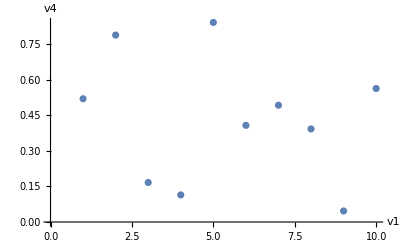

```mathematica
ListPlot[Transpose[{v1,v4}],
AxesLabel->{"v1","v4"}]
```

Let’s define an accessory function to calculate the Pearson Correlation Coefficient for all 13 features in our dataset, then perform the calculation:

```mathematica
featureCorrelation[data_]:=With[
{featureNames=Keys@First@Keys[data],
x=Keys[data],
y=Values[data]},
AssociationMap[ Correlation[Lookup[x,#],y]&]@featureNames]
```

```mathematica
featureCorrelation[train]
```

<|AromaticRingCount→0.350021,HBondDonorCount→-0.150569,HBondAcceptorCount→-0.339941,FractionCarbonSP3→-0.394641,HeteroatomCount→-0.341644,HeterocycleCount→-0.0249077,RotatableBondCount→-0.179145,MolecularMass→-0.231405,DegreeOfUnsaturation→-0.00602688,MinEllipsoidLength→0.266395,MaxDistance→0.204869,LongestPiChain→0.392929,LinkerLength→0.487279|>

We can visualize the correlations sorted by value in a Bar Chart:

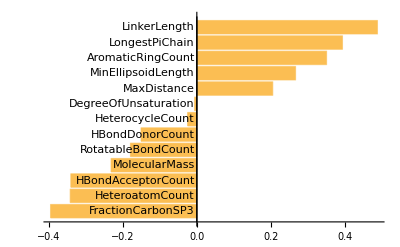

```mathematica
BarChart[
Sort@featureCorrelation[train],
ChartLabels->Automatic,BarOrigin->Left]
```

Think about which features show strong positive or negative correlations. Does your chemical intuition say that any of these properties might be physically meaningful in determining cyanine dye absorption?

### Applying Pearson Correlation

Now let’s try training a simple linear regression model using only the feature with the highest correlation. Add code blocks below to train the model, plot the predicted vs. actual wavelengths, and generate performance metrics. (Hint: as before, you can do this by copying and modify code blocks from above.) How do the results compare to your previous simple linear regression models?

ADD A CODE BLOCK TO PERFORM A SIMPLE LINEAR REGRESSION FOR A SINGLE HIGHLY CORRELATED VARIABLE, PLOT THE RESULTS, AND CALCULATE PERFORMANCE METRICS

## Regularized (or Penalized) Regression

Another approach we can take to prevent overfitting is adding a tuning parameter (regularization) that penalizes model complexity. In other words, this penalty tends to keep the model coefficients smaller and minimizes the effect of extreme values in the training dataset. These types of models are referred to as regularized or penalized regression.

https://jakevdp.github.io/PythonDataScienceHandbook/05.06-linear-regression.html#Regularization

https://en.wikipedia.org/wiki/Regularization_(mathematics)

There are several types of regularization penalties that can be applied. Let' s test two different types of regularized regression models:

Ridge Regression (a.k.a. L2 regularization)

Lasso Regression (a.k.a. L1 regularization)

### Ridge Regression

Ridge Regression uses a penalty given by a regularization parameter (which we’ll call alpha) multiplied by the sum of the squared model coefficients:

This penalty is then added to the normal RSS term. Addition of this penalty term has the effect of shrinking the model coefficients, helping to reduce model complexity and prevent overfitting.

https://jakevdp.github.io/PythonDataScienceHandbook/05.06-linear-regression.html#Ridge-regression-($L_2$-Regularization)

https://en.wikipedia.org/wiki/Ridge_regression

Let’s look how Ridge Regression performs using all the features. Note that you can tune the weight of the penalty by adjusting the alphaValueRidge parameter in the code below. Reducing alpha to 0 makes the penalty 0 and turns this model back into a normal multiple regression.

Run the code block below perform Ridge Regression analysis. (Start with the default value of alpha, but later you can test how changing alpha affects the results.)

```mathematica
alphaValueRidge=1;
```

```mathematica
ridgeRegressor1=Predict[train,
Method->{"LinearRegression","L1Regularization"->0,"L2Regularization"->alphaValueRidge}];

metrics["Ridge (1)"]=modelEvaluation[ridgeRegressor1,test]
```

<|MeanDeviation→58.7195,MeanSquare→5027.31,StandardDeviation→70.9036,RSquared→0.399745|>

It is also possible to let Mathematica attempt to automatically determine the regularization parameter by setting the value of the parameter to Automatic. (By default, if neither regularization option is specified, Mathematica’s default to L2Regularization → Automatic.)

The code block below performs automatic Ridge Regression and displays the performance metrics.

```mathematica
ridgeRegressorAuto=Predict[train,
Method->{"LinearRegression","L1Regularization"->0,"L2Regularization"->Automatic}];

metrics["Ridge (Auto)"]=modelEvaluation[ridgeRegressorAuto,test]
```

<|MeanDeviation→58.7195,MeanSquare→5027.31,StandardDeviation→70.9036,RSquared→0.399745|>

Now let’s plot the actual vs. predicted wavelength  for the test dataset with the Ridge Regression model with alphaValueRidge = 1.

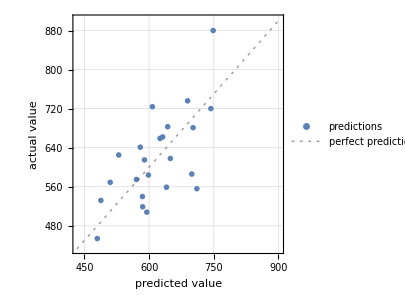

```mathematica
PredictorMeasurements[ridgeRegressor1,test,"ComparisonPlot"]
```

From the performance metrics, we can see that the Ridge Regression model performs slightly better than the the Multiple Linear Regression without a penalty in this case.

Now try tuning the value of alpha and see how it affects the results. Add a code block below to train new Ridge Regression models and test different values of alpha. (Hint: you will need to rename the variable RidgeRegressor1 to store the new models):

Test alpha = 0

Test a few intermediate values of alpha

Calculate the performance metrics for each model and compare to the results for an unpenalized multiple linear regression and the Ridge Regression with the highest penalty (alpha = 1). Which model gives the best performance?

ADD CODE BLOCKS HERE TO PERFORM RIDGE REGRESSION ANALYSIS USING DIFFERENT VALUES OF ALPHA. ALSO PLOT THE RESULTS AND CALCULATE PERFORMANCE METRICS.

### Lasso Regression

Lasso Regression uses a penalty given by a regularization parameter (again we’ll call it alpha) multiplied by the absolute value of the model coefficients:

Like for Ridge regression, this penalty term is added to the RSS term and has the effect of shrinking the model coefficients.

https://jakevdp.github.io/PythonDataScienceHandbook/05.06-linear-regression.html#Lasso-regression-($L_1$-regularization)

https://en.wikipedia.org/wiki/Lasso_(statistics)

The syntax for Lasso Regression is the same as for Ridge Regression, but this time with the “L1Regularization” parameter as the relevant hyperparameter. Try writing a code block to train a Lasso Regression model, plot the predicted vs. true wavelength, and calculate the performance metrics. Start with the maximum penalty value (alpha = 1) and then test a few different values, as you did for Ridge Regression. (Hint: be sure that you set the “L2Regularization” parameter back to 0.)

ADD A CODE BLOCK BELOW TO TRAIN A LASSO REGRESSION MODEL, PLOT THE RESULTS, AND CALCULATE PERFORMANCE METRICS. THEN DO THE SAME THING FOR A FEW DIFFERENT VALUES OF THE ALPHA PARAMETER.  ADD YOUR RESULTS TO THE metrics ASSOCIATION, AS DEMONSTRATED ABOVE.

## Model Evaluation

Let’s now review all the developed models to see which perform the best. (Remember that these results will vary each time you execute the notebook because of the random train/test split of the dataset.)

```mathematica
Dataset[metrics]
```

Ensure that the table above includes all the models that you tested. If it doesn’t, go back and save the missing performance metrics to the metrics variable.

Although the model performance isn’t perfect, you can see that choosing a well-correlated feature can give better results than a poorly-correlated feature, and that using a penalized regression model can often improve on the performance of an unpenalized multiple regression.

## Feature Importance

In addition to using a regression model to make quantitative predictions of our target value, we can also use it to gain insight into the system that we are studying. In other words, we can use regression models to generate hypotheses about what factors are important for cyanine dye absorption. One way to do this is to assess which of the independent variables make the largest contribute to determining the predicted result in our regression models. We refer to this property as feature importance.

### Feature Importance Using Coefficients

There is a simple approach for interpreting feature importance in linear regression models like the ones we’ve used so far. Coefficients with larger magnitudes correspond to features that are playing a larger role in the model. Run the code blocks below to plot the coefficients associated with each feature in the multiple regression model:

```mathematica
extractLinearModelCoefficients[model_]:=With[
{featureNames=model[[1,"Input","Preprocessor",2,"Input"]]//Keys,
weights=Information[ model[[1,"Model","MeanFunction"]], "Arrays"][[Key[{"Weights"}]]]//First//Normal},
AssociationThread[featureNames->weights]
]
```

```mathematica
resultsMR=extractLinearModelCoefficients[multipleRegression]
```

<|AromaticRingCount→0.0744718,HBondDonorCount→0.775834,HBondAcceptorCount→1.15048,FractionCarbonSP3→-0.718369,HeteroatomCount→-2.73266,HeterocycleCount→0.58016,RotatableBondCount→0.0939752,MolecularMass→0.961716,DegreeOfUnsaturation→0.340505,MinEllipsoidLength→-0.0832416,MaxDistance→0.215384,LongestPiChain→-0.382984,LinkerLength→0.445398|>

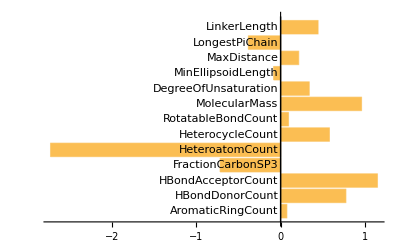

```mathematica
BarChart[resultsMR,
ChartLabels->Automatic,BarOrigin->Left]
```

To make the results even clearer, we can sort by coefficient value.

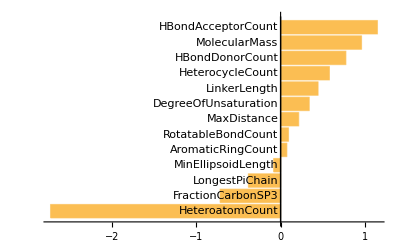

```mathematica
BarChart[ Sort[resultsMR],
ChartLabels->Automatic,BarOrigin->Left]
```

You might notice that the features with the highest weights are not the same as the features that were best correlated with the MaxAbsorbanceWavelength according to the Pearson Correlation analysis. That discrepancy can arise because the Pearson Correlation analysis looks at the correlation between each independent variable and the dependent variable separately, whereas this analysis is looking at the contribution of each independent variable to the model that includes all 13 independent variables together. This is an important caveat, and it means that sometimes feature importance analysis based on the coefficients can be misleading.

Now let’s look at the feature importance for the Ridge and Lasso Regression models. Modify the code blocks above to generate plots of the coefficients for each of those models.

ADD A CODE BLOCK BELOW TO PLOT THE FEATURE COEFFICIENTS FOR THE RIDGE AND LASSO REGRESSION MODELS WITH ALPHA = 1

## Gaining Insight from Regression Models

Look back at the results of all the regression models that you’ve trained so far. Also consider the Pearson Correlation analysis and the feature importance analysis.

None of our 13 features can fully explain the differences in wavelength of maximum absorbance for all the cyanine dyes in our dataset. But now, use your chemical intuition and try to generate a hypothesis that is grounded in quantum chemistry, using any insight that you can take from the regression models. (Hint: think about the quantum chemistry models that you’ve studied so far in your physical chemistry course.)

# Part II

## Feature Engineering

So far we’ve only considered the 13 features in our dataset. But we can also make combinations of these individual features to try to improve model performance. This process of creating new features from the ones we already have, either combining them or applying other operations, is called feature engineering.

https://jakevdp.github.io/PythonDataScienceHandbook/05.04-feature-engineering.html

https://en.wikipedia.org/wiki/Feature_engineering

Let’s try making a new feature that is the product of the number of heteroatoms and the number of heterocycles in the molecules and then use that new feature in a model.

The following adds a new feature, named HACxHCC to each row, take the current value of the row (represented by the placeholder Slot variable #) , looking up the value of the named columns in each row.

```mathematica
expandedDataset=dataset[All, 
<|#,"HACxHCC"->#["HeteroatomCount"]*#["HeterocycleCount"]|>&];
```

Now repeat this process by combining two or more features of your choice (by addition, multiplication, subtraction, etc). For example, you could pick two of the features with highest correlation in the Pearson analysis, or you could pick two features that your chemical intuition says might be important. Add a code block below to generate a new feature.

ADD A CODE BLOCK BELOW TO CREATE A NEW FEATURE BY COMBINING FEATURES FROM THE ORIGINAL DATASET

Now try running simple linear regression analyses separately with HACxHCC and your new feature. You will need to go through the preprocessing data steps (separating x and y values, splitting, rescaling, etc) before performing the regression.

ADD A CODE BLOCK BELOW TO REPEAT THE DATA PREPROCESSING, PERFORM A SIMPLE LINEAR REGRESSION FOR THE TWO NEW FEATURES, VISUALIZE THE RESULTS, AND CALCULATE PERFORMANCE METRICS

How well did HACxHCC and your new feature perform?

## Tree Models

Tree models make decisions using a tree-like structure with nodes, branches, and leaves. They can be used for either regression or classification analyses.

The most common tree-based models for regression problems are:

Decision Tree

Random Forest

### Decision Tree Regression

The Decision Tree algorithm uses a single tree to make predictions. It models the data in a tree structure in which each leaf node leads to the prediction for the dependent variable. Although easy to implement, Decision Tree models can be prone to overfitting.

https://jakevdp.github.io/PythonDataScienceHandbook/05.08-random-forests.html

https://en.wikipedia.org/wiki/Decision_tree_learning

The code block below trains a Decision Tree model and visualizes the tree structure. Run this analysis, then add a code block to plot the predicted vs. actual wavelength and to calculate the performance metrics.

```mathematica
decisionT=Predict[train,Method->"DecisionTree"]
```

PredictorFunction[…]

Let’s visualize how well this model fits the training data:

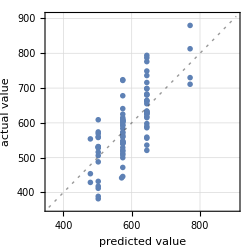
Predictor Measurements
Predictor method | DecisionTree
Number of test examples | 92
Standard deviation | 65.9 ± 4.6
Standard deviation baseline | 96.2 ± 7.6
R-squared | 0.531 ± 0.099
Mean cross entropy | 5.59 ± 0.071
Single evaluation time | 11.1 ms/example
Batch evaluation speed | 649. examples/s
-Graphics- |

```mathematica
PredictorMeasurements[decisionT,train]
```

Now let’s visualize how well this model predicts the test data:

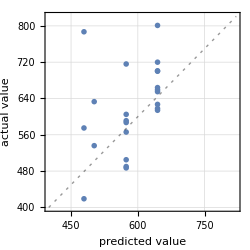
Predictor Measurements
Predictor method | DecisionTree
Number of test examples | 23
Standard deviation | 94.7 ± 23.
Standard deviation baseline | 93.3 ± 13.
R-squared | -0.0307 ± 0.57
Mean cross entropy | 6.13 ± 0.46
Single evaluation time | 7.61 ms/example
Batch evaluation speed | 366. examples/s
-Graphics- |

```mathematica
PredictorMeasurements[decisionT,test]
```

Now add a code block to include the performance metrics for the Decision Tree regression in our metrics Association.

ADD A CODE BLOCK HERE TO PLOT THE DECISION TREE RESULTS AND CALCULATE PERFORMANCE METRICS

### Random Forest Regression

Random Forest builds a collection of Decision Trees, where each tree is trained with a random subset of training instances and a random subset of features. The final prediction is determined as the average output among the collection of trees. The Random Forest algorithm is less prone to overfitting data than the Decision Tree algorithm.

https://jakevdp.github.io/PythonDataScienceHandbook/05.08-random-forests.html#Random-Forest-Regression

https://en.wikipedia.org/wiki/Random_forest

To train a Random Forest model, you can simply change the “Method” to “RandomForest” in the Predict function. Add a code block below to train a Random Forest model, plot the predicted vs. actual wavelength, and calculate the performance metrics.

ADD A CODE BLOCK HERE TO TRAIN A RANDOM FOREST MODEL, PLOT THE RESULTS, RESULTS AND CALCULATE PERFORMANCE METRICS

### Feature Importance using SHapley Additive exPlanations (SHAP)

For the linear regression models in Part I of this activity, we used the coefficients to determine which features were most important in the model. But for non-linear models, like DecisionTree or RandomForest, determining feature importance can be more difficult. There are a few model-specific approaches that can be used, but here we will implement a general approach called SHapley Additive exPlanations (SHAP).

SHAP is a method derived from Game Theory (a topic in Economics) that brings interpretability to machine learning models, showing the contribution of each feature in a model-agnostic way. For more information see:

Original report (“A Unified Approach to Interpreting Model Predictions” by Scott M. Lundberg and Su-In Lee): https://papers.nips.cc/paper/2017/hash/8a20a8621978632d76c43dfd28b67767-Abstract.html

https://shap.readthedocs.io/en/latest/index.html

### SHAP Analysis for Decision Tree Regression

Now let’s try to understand our Decision Tree model using the SHAP approach. The code block below performs SHAP analysis on our Decision Tree model and displays a plot of feature importance:

```mathematica
(*note: the "Quiet" below suppresses error messages that aren't important for the results*)
shapPlotDecisionT=PredictorMeasurements[decisionT,train,"SHAPPlots"]//Quiet
```

-Graphics-

The plot above can be interpreted by looking at the distance from the Feature Impact = 0 line and the displayed color of each point. The distance from the 0 line reflects how much of an impact the feature had on the model for that particular data point. The displayed color shows whether the feature value was low/more negative (blue) or high/more positive (yellow) for that point. Features with points more distant from the 0 line were more important for the model. When points of the same color cluster on one side of the 0 line, it indicates that the feature value tended to shift the model prediction in a more consistent direction.

It can be simpler to omit the effect direction and just calculate the absolute value of the SHAP value for each feature. We can write a convenience function to extract the SHAP values for each feature, take the absolute values, and calculate the average.

```mathematica
shapSummary[model_PredictorFunction,data_]:=With[
{shapVals= Dataset@PredictorMeasurements[model,data,"SHAPValues"]},
shapVals[Mean][Abs]//Normal//Sort]
```

Now let’s calculate the mean absolute SHAP values for the Decision Tree regression and display them in a bar plot:

```mathematica
(*calculate mean absolute SHAP values*)
SHAPresultDecisionT=shapSummary[decisionT,train]
```

<|AromaticRingCount→0.188365,LongestPiChain→0.502222,HeterocycleCount→0.718583,HeteroatomCount→0.80875,MolecularMass→0.878496,HBondAcceptorCount→1.00663,RotatableBondCount→1.12681,HBondDonorCount→2.00391,MinEllipsoidLength→2.05409,LinkerLength→2.20562,MaxDistance→2.36768,DegreeOfUnsaturation→7.9276,FractionCarbonSP3→16.5769|>

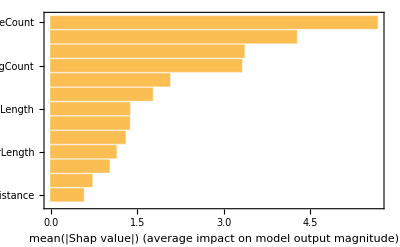

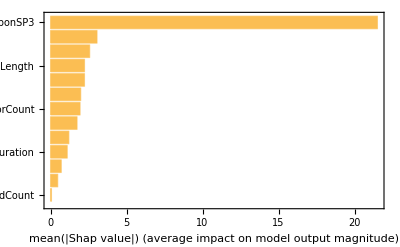

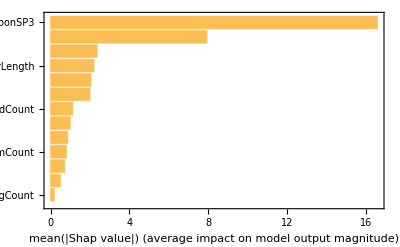

```mathematica
BarChart[SHAPresultDecisionT,
ChartLabels->Automatic,BarOrigin->Left,
Frame->True,FrameLabel->"mean(|Shap value|) (average impact on model output magnitude)"]
```

### SHAP Analysis for Random Forest Regression

Now follow the same approach to interpret our Random Forest model using the SHAP approach. Add a code block below to perform SHAP analysis and plot the results.

ADD A CODE BLOCK HERE TO PERFORM SHAP ANALYSIS FOR THE RANDOM FOREST MODEL AND GENERATE PLOTS OF FEATURE IMPORTANCE

Are these tree models relying on the same features as the linear regression models above?

# Conclusion

This exercise is just one example of how machine learning regression analysis can be applied to chemistry. As you continue in your chemistry studies or research, look for other opportunities to make predictions or generate hypotheses using these types of models!